```mathematica
<<mf23.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m; so A(m) does not appear in the expansions. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
JnewCffList[6,3,x]
```

{1,744,196884,21493760,864299970,20245856256}

```mathematica
For[m=2,m<6,m++;
Print[J[5,m,X]]]
```

31/72+1/X+(1823 X)/27648+(10495 X^2)/2519424+(1778395 X^3)/18345885696

13/32+1/X+(1093 X)/16384+(47 X^2)/8192+(620001 X^3)/2147483648

79/200+1/X+(42877 X)/640000+(12957 X^2)/2000000+(1335816657 X^3)/3276800000000

7/18+1/X+(29 X)/432+(271 X^2)/39366+(269 X^3)/559872

```mathematica
For[m=2,m<6,m++;
Print[xJ[5,m,X]]]
```

1+(31 X)/72+(1823 X^2)/27648+(10495 X^3)/2519424+(1778395 X^4)/18345885696

1+(13 X)/32+(1093 X^2)/16384+(47 X^3)/8192+(620001 X^4)/2147483648

1+(79 X)/200+(42877 X^2)/640000+(12957 X^3)/2000000+(1335816657 X^4)/3276800000000

1+(7 X)/18+(29 X^2)/432+(271 X^3)/39366+(269 X^4)/559872

#### The functions below are Raleigh’s interpolating rational functions (p. 108). My code recovers them!

```mathematica
stream=OpenWrite["run20apr21no3"];
start=SessionTime[];
For[m=2,m<300,m++;
expansion=J[100,m,x];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 7240.140855

#### “run20apr21no3” is too large for github. I am going to create several shorter files.

```mathematica
rstream=OpenRead["run20apr21no3"];
list=ReadList[rstream];
Close[rstream];
Length[list]
```

298

```mathematica
rstream=OpenRead["run20apr21no3"];
list=ReadList[rstream];
Close[rstream];
wstream1=OpenWrite["run2jun21no11"];
For[j=0,j<50,j++;
Write[wstream1,list[[j]]]];
Close[wstream1];
wstream2=OpenWrite["run2jun21no12"];
For[j=0,j<50,j++;
Write[wstream2,list[[j+50]]]];
Close[wstream2];
wstream3=OpenWrite["run2jun21no13"];
For[j=0,j<50,j++;
Write[wstream3,list[[j+100]]]];
Close[wstream3];
wstream4=OpenWrite["run2jun21no14"];
For[j=0,j<48,j++;
Write[wstream4,list[[j+150]]]];
Close[wstream4]
```

run2jun21no14

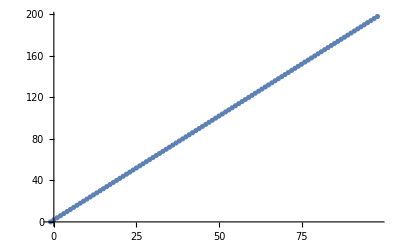

run20apr21no5

```mathematica
stream=OpenRead["run20apr21no3"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run20apr21no5"];
degrees={};
For[n=-2,n<98,n++;
data={};
For[k=0,k<298,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf*m^(2*n+2)}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
Length[list]
```

100

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
lastm=Last[list][[1]];
Print[{lastm,Length[list]}]
```

{98,100}

#### Check Raleigh’s first paper, p. 108, equation (III):

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
For[k=0,k<5,k++;
index=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
fm=factorIntoMonics[poly];
Print["================================================"];
Print["index: ",index];
Print[poly];
Print[fm]]
```

================================================

index: -1

1

{1}

================================================

index: 0

4+3 x^2

{3/8,4/3+x^2}

================================================

index: 1

-48-8 x^2+69 x^4

{69/1024,-16/23-(8 x^2)/69+x^4}

================================================

index: 2

-16-8 x^2+27 x^4

{1/128,-2+x,2+x,-16/27-(8 x^2)/27+x^4}

================================================

index: 3

19392+11312 x^2-38732 x^4+5601 x^6

{5601/8388608,-2+x,2+x,6464/1867+(11312 x^2)/5601-(38732 x^4)/5601+x^6}

```mathematica
stream=OpenRead["run28apr21no5"];
list=ReadList[stream];
Close[stream];
yes1=0;
no1=0;
yes2=0;
no2=0;
yes3=0;
no3=0;
yes4=0;
no4=0;
yes5=0;
no5=0;
yes6=0;
no6=0;


For[j=0,j<Length[list],j++;
Clear[poly];
n=list[[j,1]];
If[n>1,
poly0=list[[j,2]];
list2=factorIntoMonics[poly0];
last=Last[list2];
If[monicPolynomialQ[last,x]==True,yes1++];
If[monicPolynomialQ[last,x]==False,no1++];
If[IrreduciblePolynomialQ[last]==True,yes2++];
If[IrreduciblePolynomialQ[last]==False,no2++];
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes3++];
If[Not[AllTrue[cl,rationalQ]],no3++];
degree=Exponent[last,x];
If[degree==2*n,yes4++];
If[degree≠2*n,no4++];
deglast=Exponent[last,x];
bad=0;
For[k=-1,k<deglast,k++;
cfk=Coefficient[last,x,k];
If[Mod[k,2]==0&&cfk==0,bad++];
If[Mod[k,2]==1&&cfk≠0,bad++]
];
If[bad==0,yes5++];
If[bad≠0,no5++];
If[Length[list2]==4&&list2[[2]]==-2+x&&list2[[3]]==2+x,yes6++];
If[Length[list2]!=4,no6++]
]

];
Print[{{yes1,no1},{yes2,no2},{yes3,no3},{yes4,no4},{yes5,no5},{yes6,no6}}]
```

{{97,0},{97,0},{97,0},{97,0},{97,0},{97,0}}